302909.

-40701.6

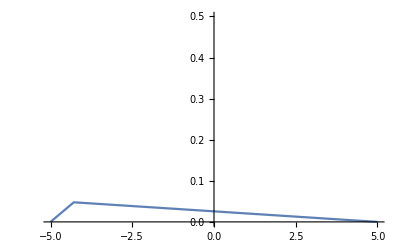

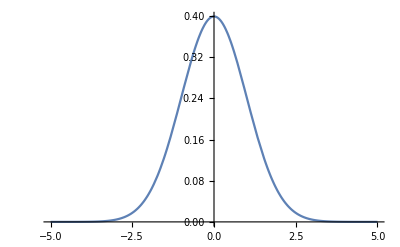

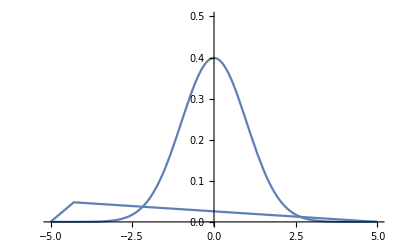

```mathematica
data=Import["/home/petergu/MyHome/USTCcomputer/2019Autumn/CompPhys/HW9/data.csv"];
data=Flatten[data];
Max[data]
Min[data]
(*Histogram[data,{1},PlotRange->{{-100,100},{0,10000}}]*)
p=SmoothHistogram[data,PlotRange->{{-5,5},{0,.5}}]
real=Plot[1/(√(2π))Exp[-x^2/2],{x,-5,5},PlotRange->All]
Show[p,real]
```